```mathematica
g=Cos[π ϕ/σ/2]^2*HeavisideTheta[σ-Abs[ϕ]]
```

```mathematica
Integrate[Cos[π ϕ/σ/2]^4,{ϕ,-σ,σ}]
```

(3 σ)/4

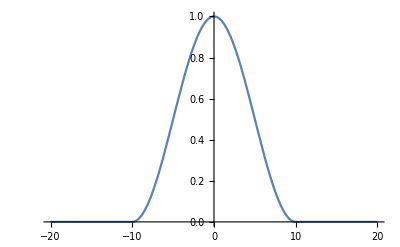

```mathematica
Plot[g/.σ->10,{ϕ,-20,20}]
```

```mathematica
FT=FourierTransform[g*Exp[-I*ϕ]*Sqrt[2*π],ϕ,L,Assumptions->{σ>0}]
```

(ⅈ π^2 (Cos[2 σ]-Cos[2 L σ]+ⅈ Sin[2 σ]-ⅈ Sin[2 L σ]) (Cos[(1+L) σ]-ⅈ Sin[(1+L) σ]))/(2 (-1+L) (π^2-(-1+L)^2 σ^2))

```mathematica
FT^2
R=Simplify[%]
```

-(π^4 (Cos[2 σ]-Cos[2 L σ]+ⅈ Sin[2 σ]-ⅈ Sin[2 L σ])^2 (Cos[(1+L) σ]-ⅈ Sin[(1+L) σ])^2)/(4 (-1+L)^2 (π^2-(-1+L)^2 σ^2)^2)

(π^4 Sin[σ-L σ]^2)/((-1+L)^2 (π^2-(-1+L)^2 σ^2)^2)

```mathematica
π/4/ArcCos[1/2^(1/4)]//N
```

1.37341

```mathematica
Integrate[Exp[-x^2/w^2],{x,-Infinity,Infinity},Assumptions->{w>0}]
```

√π w

```mathematica
Integrate[R,{L,-Infinity,Infinity},Assumptions->{σ>0}]
```

ConditionalExpression[(3 π σ)/2, σ<π]